### function(s)

```mathematica
Needs["PlotLegends`"];
SetDirectory["/home/moosmann/mathematica/multileptons"];

mu=105.658369 10^6 ; (*muon mass*)

(*Substitute x1 by x2 using the expression for the invariant mass*)
Block[{solx1m},
{solx1p,solx1m}=Evaluate[x1/.Simplify[Solve[X^2==2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]]];
solx1p];

(*condition for x1=f(x2,X,cos(θ)) to be real and positiv*)
solx1sqrtcon=Boole[(-4 X^2+X^4+4 (-1+cos^2) x2^2)>0];

(*Jacobian determinant jx1Xp=(d/dx1 X^2)^-1 with x1 substituted by solx1p, where X^2 is given by the dimless invariant mass and dx1=2*X*jx1Xp*dX *)
jx1Xp=Simplify[1/D[2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]/.x1->solx1p];

(*relative angle condition*)
Block[{n},
n[cos_,p_]:={Sqrt[1-cos^2]Cos[2π p],Sqrt[1-cos^2]Sin[2π p],cos};
cos12=n[cos1,p1]. n[cos2,p2];
angcon=Boole[Evaluate[cos12]>cosmin];
]

(*transversal impuls cut-off*)
ptcut=Boole[(1-cos1^2)x1^2>((ptmin  10^9)/mu)^2]*Boole[(1-cos2^2)x2^2>((ptmin  10^9)/mu)^2]/.{x1->solx1p};

(* function that gives the data to plot {X,#f/ΔX} *)
Remove[plotdata];
plotdata[yy_,CosMin_,acgoal_,prgoal_,partlist_,Xmax_,points_,pt_]:=
Block[{dX=(Xmax-2)/points,y=yy,cosmin=CosMin,ptmin=pt,cos=cos12,plot,int,time},

int= Evaluate[
ptcut angcon solx1sqrtcon jx1Xp
 solx1p^3/Sqrt[solx1p^2+1] 1/(Exp[1/(11.24/(2π)y) Sqrt[1+solx1p^2]]+1) 
x2^3/Sqrt[x2^2+1] 1/(Exp[1/(11.24/(2π)y) Sqrt[1+x2^2]]+1)
];


Table[{X,
16(*remove Lambert's Law factor*)2X (*change from dx1->dX*)(2π)^2(*change from ϕ->2πp*)(1/(8 π^3))^2(*original prefactor*)NIntegrate[
int,
{x2,0,Sqrt[X^2(X^2-1)/4]},{cos1,-1,1},{cos2,-1,1},{p1,0,1},{p2,0,1},
Method->{"AdaptiveQuasiMonteCarlo","Partitioning"->partlist},
AccuracyGoal->acgoal,
PrecisionGoal->prgoal
]},{X,2,Xmax,dX}
]

];
```

### data

#### y = 1, cos = -1

```mathematica
Timing[y10cosM1pt0=plotdata[1,-1,2,2,6,20,100,0];]
```

{39916.1,Null}

```mathematica
Timing[y10cosM1pt1=plotdata[1,-1,2,2,6,40,100,1];]
```

{40763.3,Null}

#### y = 1, cos = .8

```mathematica
Timing[y10cos08ptcut0=plotdata[1,.8,2,2,6,10,100,0];]
```

{38756.7,Null}

```mathematica
Timing[pdaty10cos08ptcut1=plotdata[1,.8,2,2,6,15,100,1];]
```

{39965.2,Null}

#### y = .5, cos = -1

```mathematica
Timing[y05cosM1pt0=plotdata[.5,-1,2,2,3,20,100,0];]
```

{1235.85,Null}

```mathematica
Timing[y05cosM1ptcut1=plotdata[.5,-1,2,2,3,40,100,1];]
```

{1287.81,Null}

#### y = .5, cos = .8

```mathematica
Timing[y05cos08pt0=plotdata[.5,.8,2,2,3,10,100,0];]
```

{1186.01,Null}

```mathematica
Timing[y05cos08pt1=plotdata[.5,.8,2,2,3,15,100,1];]
```

{1177.64,Null}

### plots

#### single plot

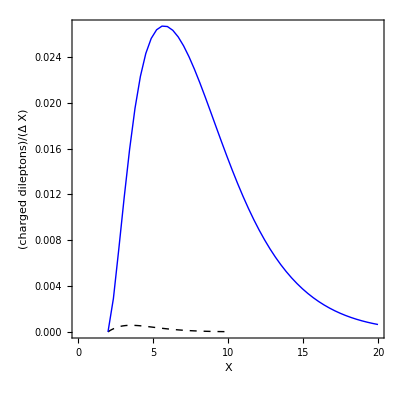

```mathematica
ShowLegend[
ListPlot[{pdaty05cosM1ptcut0,pdaty10cosM1ptcut0},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Black,Dashed},{Blue}},
Frame->True,FrameLabel->{"X","(charged dileptons)/(Δ X)"},FrameTicks->{{All,None},{All,None}},
AxesOrigin->{0,0},AspectRatio->1]
,{{{Graphics[{Blue,Line[{{0,0},{1.5,0}}]}],"y = 1"},{Graphics[{Black,Dashed,Line[{{0,0},{1.5,0}}]}],"y = .5"}},LegendPosition->{1.1,-.4}}
]
```

#### test

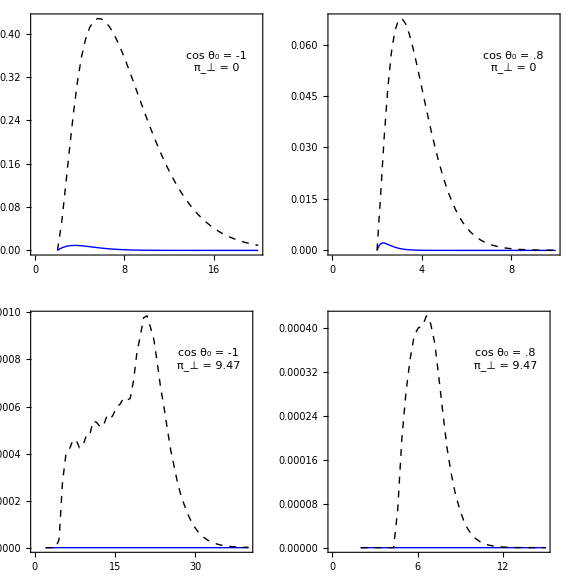

```mathematica
GraphicsGrid[{{
ListPlot[{pdaty05cosM1ptcut0,pdaty10cosM1ptcut0},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 0"}}],10]],Scaled[{.8,.8}]]],
ListPlot[{pdaty05cos08ptcut0,pdaty10cos08ptcut0},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 0"}}],10]],Scaled[{.8,.8}]]]
},{
ListPlot[{pdaty05cosM1ptcut1,pdaty10cosM1ptcut1},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]],
ListPlot[{pdaty05cos08ptcut1,pdaty10cos08ptcut1},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]]
}},ImageSize->Large]
```

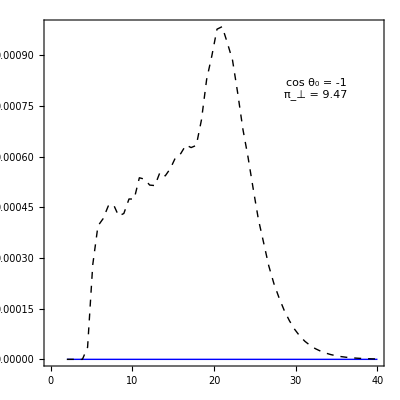

```mathematica
ListPlot[{pdaty05cosM1ptcut1,pdaty10cosM1ptcut1},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]]
```

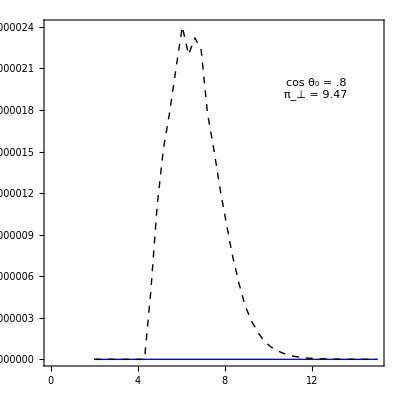

```mathematica
ListPlot[{pdaty05cos08ptcut1,pdaty10cos08ptcut1},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]]
```

#### multi plots

```mathematica
Block[{plot,lamb,l},

lamb[list_List]:=Block[{},
l=Length@list;
Table[{1,1}list[[i]],{i,1,l}]];

plot=ShowLegend[
GraphicsGrid[{{
ListPlot[{lamb@y05cosM1pt0,lamb@y10cosM1pt0},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 0"}}],10]],Scaled[{.8,.8}]]],
ListPlot[{lamb@y05cos08pt0,lamb@y10cos08ptcut0},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 0"}}],10]],Scaled[{.8,.8}]]]
},{
ListPlot[{lamb@y05cosM1ptcut1,lamb@y10cosM1pt1},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]],
ListPlot[{lamb@y05cos08pt1,lamb@pdaty10cos08ptcut1},
PlotRange->All,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]]
}},ImageSize->Large]
,{{{Graphics[{Black,Dashed,Line[{{0,0},{1.5,0}}]}],"y = 1"},{Graphics[{Blue,Line[{{0,0},{1.5,0}}]}],"y = .5"}},LegendPosition->{1.1,-.250},LegendSize->{.3,.5}}
];

Export["dilepton-spectrum-new.eps",Evaluate@Labeled[plot,X,{Bottom,Left}],"eps"];

plot
]
```

-Graphics-

#### diverse plots

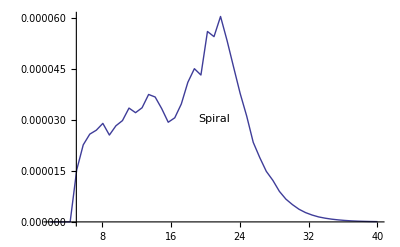

```mathematica
ListPlot[pdaty10cosM1ptcut1,PlotRange->All,Joined->True,
Epilog->Inset[Framed[Style["Spiral",10]],Scaled[{.8,.8}]]]
```

```mathematica
Timing[pdaty10cosM1ptcut1=plotdata[1,-1,2,2,{3,3,3,3,3},40,50,1];]
```

{612.25,Null}

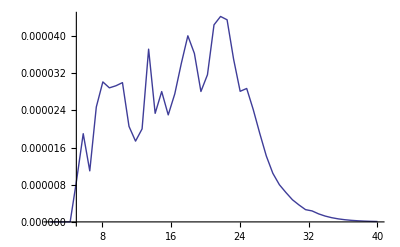

```mathematica
ListPlot[plotdata[1,-1,2,2,{2,2,2,2,2},40,50,1],PlotRange->All,Joined->True]
```

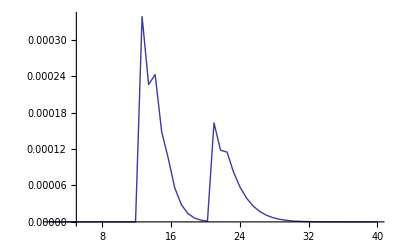

```mathematica
ListPlot[plotdata[1,-1,1,1,{1,1,1,1,1},40,50,1],PlotRange->All,Joined->True]
```

### prefactor stuff

```mathematica
(* energy per unit time and surface / m^4 *)
JTH[y_,x0_]:=1/(4 π^2)*NIntegrate[x^3/(Exp[2π/(11.24 y)x]+1)+2 x^3/(Exp[2π/(11.24y)Sqrt[1+x^2]]+1),{x,0,x0},MaxRecursion->100];
(* prefactor*m^3 to multiplied with fermion spectrum to yield the total number of fermions *)
prefactor[y_,d_:1,ECOM_:1 10^12]:=1/mu 4π  (d ECOM/mu)/(4π JTH[y,100]);
```

```mathematica
prefactor[1]
```

2204.06

```mathematica
prefactor[.5]
```

38230.

#### testing

```mathematica
TableForm@Table[JTH[y,10^x],{y,{.1,.5,1}},{x,-1,6}]
```

2.51742×10^-7 | 0.000128627 | 0.000167159 | 0.000167159 | 0.000167159 | 0.000167159 | 0.000167159 | 0.000167159
6.13652×10^-7 | 0.00427993 | 0.246355 | 0.247566 | 0.247566 | 0.247566 | 0.247566 | 0.247566
7.69736×10^-7 | 0.00661962 | 3.41345 | 4.29411 | 4.29411 | 4.29411 | 4.29411 | 4.29411

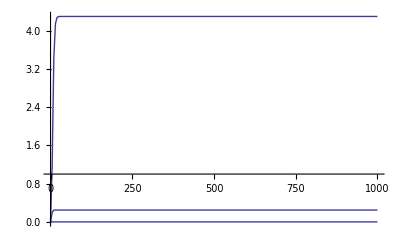

```mathematica
Plot[Table[JTH[y,x0],{y,{.1,.5,1}}],{x0,0,1000},PerformanceGoal->"Speed",PlotRange->All,AxesOrigin->{0,1}]
```

### partition testing

```mathematica
SetDirectory["/home/moosmann/mathematica/multileptons/plots"]
```

/home/moosmann/mathematica/multileptons/plots

#### function

```mathematica
Remove[plotfun,plotfuntest];
plotfun[y_,cosmin_,ptcut_,Xrange_]:=
Block[{plot,graf},

plot[partition_]:=Block[{t,dat},
{t,dat}=Timing@plotdata[y,cosmin,2,2,partition,Xrange,50,ptcut];
Print[TableForm[{{"done: ",partition}}]];
ListPlot[dat,
PlotRange->All,PerformanceGoal->"Quality",Joined->True,Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,Epilog->Inset[N[t/60],Scaled[{.8,.8}]]]
];

graf=Labeled[
GraphicsGrid[{{plot[1],plot[2],plot[3]},{plot[4],plot[5],plot[6]}},ImageSize->Large],
"y ="<>ToString@y<>",   cos ="<>ToString@cosmin<>",   ptcut ="<>ToString@ptcut
];

Export["y"<>ToString[y]<>"cos"<>ToString[cosmin]<>"pt"<>ToString[ptcut],graf,"eps"];

graf

];

plotfuntest[y_,cosmin_,ptcut_,Xrange_,points_]:=
ListPlot[plotdata[y,cosmin,1,1,{1,1,1,1,1},Xrange,points,ptcut],
PlotRange->All,PerformanceGoal->"Quality",Joined->True,Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,Epilog->Inset[N[t/60],Scaled[{.8,.8}]]]
```

#### evaluation

```mathematica
plotfun[1,-1,0,25];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[1,.8,0,10];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[1,-1,1,40];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[1,.8,1,15];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,-1,0,25];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,.8,0,10];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,-1,1,40];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,.8,1,15];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[1,-1,3,100];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[1,.8,3,30];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[1,-1,5,55];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[1,.8,5,30];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,-1,3,100];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,.8,3,40];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,-1,5,70];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

```mathematica
plotfun[.5,.8,5,50];
```

done:  | 1

done:  | 2

done:  | 3

done:  | 4

done:  | 5

done:  | 6

### console mode

```mathematica
Remove[mu,solx1p,solx1sqrtcon,jx1Xp,cos12,angcon,ptcut,plotdata,plotfun];
mu=105.658369 10^6 ;
Block[{solx1m},{solx1p,solx1m}=Evaluate[x1/.Simplify[Solve[X^2==2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]]];];
solx1sqrtcon=Boole[(-4 X^2+X^4+4 (-1+cos^2) x2^2)>0];
jx1Xp=Simplify[1/D[2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]/.x1->solx1p];
Block[{n},n[cos_,p_]:={Sqrt[1-cos^2]Cos[2π p],Sqrt[1-cos^2]Sin[2π p],cos};
cos12=n[cos1,p1]. n[cos2,p2];angcon=Boole[Evaluate[cos12]>cosmin];];
ptcut=Boole[(1-cos1^2)x1^2>((ptmin  10^9)/mu)^2]*Boole[(1-cos2^2)x2^2>((ptmin  10^9)/mu)^2]/.{x1->solx1p};
plotdata[yy_,CosMin_,partlist_,Xmax_,points_,pt_]:=
Block[{dX=(Xmax-2)/points,y=yy,cosmin=CosMin,ptmin=pt,cos=cos12,plot,int,time},
int= Evaluate[ptcut angcon solx1sqrtcon jx1Xp solx1p^3/Sqrt[solx1p^2+1] x2^3/Sqrt[x2^2+1] 1/(Exp[1/(11.24/(2π)y) Sqrt[1+x2^2]]+1)];
Table[{X,16(2π)^2(1/(8 π^3))^2 NIntegrate[int,{x2,0,Sqrt[X^2(X^2-1)/4]},{cos1,-1,1},{cos2,-1,1},{p1,0,1},{p2,0,1},
Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2]},{X,2,Xmax,dX}]];
plotfun[y_,cosmin_,ptcut_,Xrange_]:=
Block[{plot},plot[partition_]:=Block[{t,dat},{t,dat}=Timing@plotdata[y,cosmin,partition,Xrange,50,ptcut];Print[TableForm[{{"done: ",partition,"in ",N[t/60],"min"}}]];
ListPlot[dat,PlotRange->All,Frame->True,AxesOrigin->{0,0},AspectRatio->1]];
Table[Export["y"<>ToString[y]<>"cos"<>ToString[cosmin]<>"pt"<>ToString[ptcut]<>"part"<>ToString[part],plot[part],"eps"],{part,1,1}];]
```